```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];
SetOptions[EvaluationNotebook[],NotebookEventActions->{"WindowClose":>FrontEndExecute[FrontEndToken["DeleteGeneratedCells"]]}];
```

```mathematica
countryname="United States"; 
data=Import["DataSheet_cddep.xlsx",{"Data",countryname}];
data = data[[All,2;;]];
years = data[[1]];
tt = Length[years];
nop = (Length[data]-4)/2; (*# of bacterial strains*)
isolates = data[[2;;Length[data]-3;;2]];
resistance = data[[3;;Length[data]-3;;2]];
rfreq =resistance/isolates;
carbcons = data[[-3]]/10000; (*consumption data from cddep*)
conbreak = data[[-2,1;;nop]]; (*breakdown of consumption by bacterial strain*)
cardiv =Table[carbcons*conbreak[[i]],{i,1,nop}]; (*consumption for each bacterial strain*)
pc =  data[[-1,1]]; (*proportion of carbapanem prescription out of all antibiotics prescribed for bacterial pneuomonia NOTE: Update with better estimate. [CURRENT]=assuming empirical prescription only*)
tc = cardiv/pc; (*Total antibiotics prescribed for bacterial pneumonia.*)
prop = cardiv/tc;
diff=tc-cardiv;
```

```mathematica
(*tested this with KP data ONLY*)
isolates1=isolates[[1]];
resistance1=resistance[[1]];
nonresistant=isolates1-resistance1;
consum1=cardiv[[1]];
```

```mathematica
res[t_,a0_,rc_,rn_]:=a0*ⅇ^(rc* Total[consum1[[1;;t]]]+rn*t) (* # resistant=A *)
```

```mathematica
nres[t_,b0_,nc_,nn_]:=b0*ⅇ^(nc*Total[consum1[[1;;t]]]+nn*t) (* # not resistant=B *)
```

```mathematica
lsq[a0_,rc_,rn_]:= Total[Table[Abs[(resistance1[[j]]-res[j,a0,rc,rn])],{j,1,tt}]] (* Least squares likelihood for A *)
```

```mathematica
nlsq[b0_,nc_,nn_]:=Total[Table[Abs[(nonresistant[[j]]-nres[j,b0,nc,nn])],{j,1,tt}]] (* Least squares likelihood for B *)
```

```mathematica
{min,{a0f,rcf,rnf}}=NMinimize[{lsq[a0,rc,rn], rc>0}, {a0,rc,rn}]  (*min for A*)
```

{415.911,{a0→11.4498,rc→28.3164,rn→0.18567}}

```mathematica
{min,{b0f,ncf,nnf}}=NMinimize[{nlsq[b0,nc,nn],b0>0,nc<0}, {b0,nc,nn}]  (*min for B; unbounded*)
```

{2983.16,{b0→2596.,nc→-275.539,nn→0.398932}}

```mathematica
frn=rnf[[2]];
frc=rcf[[2]];
fa0=a0f[[2]];
fb0=b0f[[2]];
fnn=nnf[[2]];
fnc=ncf[[2]];
frn-fnn (*b*)
frc-fnc (*a*)
```

-0.213261

303.855

```mathematica
t=Range[1,tt];
a=Table[res[j,fa0,frc,frn],{j,1,tt}]
b=Table[nres[j,fb0,fnc,fnn],{j,1,tt}]
```

{14.1158,17.4761,21.7646,27.1284,33.8998,42.5049,53.5197,67.5028,85.4275,108.386,137.631,175.21,223.238}

{3073.45,3492.23,3746.25,3985.85,4137.5,4156.04,4006.6,3799.56,3486.71,3121.7,2772.03,2401.58,2063.6}

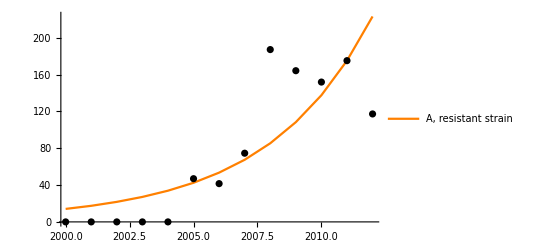

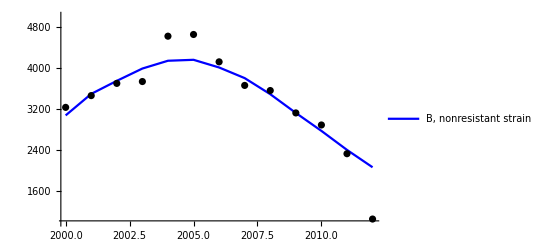

```mathematica
freq=Transpose@{years,rfreq[[1]]};
resfit=Transpose@{years,a};
resdat=Transpose@{years,resistance1};
nresfit=Transpose@{years,b};
nresdat=Transpose@{years,nonresistant};
Show[ListLinePlot[{resfit},PlotStyle-> {Orange,Thick},PlotLegends-> {"A, resistant strain"}],ListPlot[{resdat},PlotStyle-> {Black, Large}]]
Show[ListLinePlot[{nresfit},PlotStyle-> {Blue,Thick},PlotRange-> {1000,5000},PlotLegends-> {"B, nonresistant strain"}],ListPlot[{nresdat},PlotStyle-> {Black,Large},PlotRange-> {1000,5000}]]
```

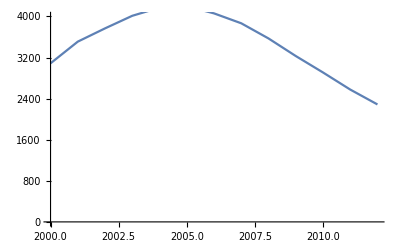

```mathematica
sum=Transpose@{years,a+b};
Show[ListLinePlot[sum],PlotRange-> {0,4000}, AxesOrigin-> {2000,0}]
```

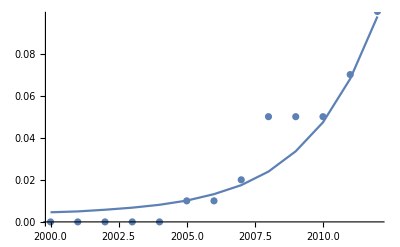

```mathematica
r=Transpose@{years,(a/(a+b))};
Show[ListLinePlot[r],ListPlot[freq]]
```